1.26888×10^-11

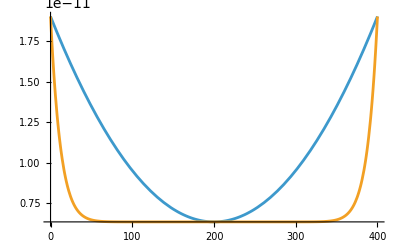

6.34442×10^-12

6.34442×10^-12

```mathematica
Dw=0.1;
Dr=2000;
mu =0.005;
k=1*10^-13;
Lw=400;
Kvw=2*Pi*k/(mu*Log[Dr/Dw])
K2[x_]:=4*Kvw*(x/Lw)^2-4*Kvw*(x/Lw)+3*Kvw/2
K[x_]:=Kvw*(2*x/Lw-1)^16+(1/2)*Kvw
Plot[{K2[x],K[x]},{x,0,Lw}]
K2[200]
K[200]
```